```mathematica
Getcoset[p_,n_]:=Module[{i,a,g},
a = ConstantArray[0,Factorial[n]];
g = Sort[GroupElements[SymmetricGroup[n]]];
For[i=1,i<= Factorial[n],i++, a[[i]] = PermutationProduct[p,g[[i]]];];
a
];
CreateG2[n_, p_, q_]:=
Module[{P,Q, U},
P=IdentityMatrix[Factorial[n]][[#]]&/@PermutationList[PermutationCycles[Ordering[Getcoset[p,n]]],Factorial[n]];
Q=IdentityMatrix[Factorial[n]][[#]]&/@PermutationList[PermutationCycles[Ordering[Getcoset[q,n]]],Factorial[n]];
U = ArrayFlatten[({{P, P}, {Q, -Q}})]/Sqrt[2]
];
CreateGX[n_, p_, q_]:=
Module[{P,Q, U},
P=IdentityMatrix[Factorial[n]][[#]]&/@PermutationList[PermutationCycles[Ordering[Getcoset[p,n]]],Factorial[n]];
Q=IdentityMatrix[Factorial[n]][[#]]&/@PermutationList[PermutationCycles[Ordering[Getcoset[q,n]]],Factorial[n]];
U = ArrayFlatten[({{P, ⅈ*P}, {ⅈ*Q, Q}})]/Sqrt[2]
];
Evolution[t_, n_,  U_,phi0_]:=
Module[{ alpha, dist,phi}, 
phi = MatrixPower[U,t].phi0;
alpha = Partition[Abs[phi]^2,Factorial[n]];
alpha[[1]]+alpha[[2]]
];

TimeAverage[T_, n_, s_]:=
Module[{i,Pt, aPt,phi,U, temp},
U = N[CreateG2[n,Cycles[{{1,2}}],Cycles[{Range[1,Factorial[n]]}]]];
phi = ConstantArray[0,2Factorial[n]];
phi[[s]] = 1;
Pt = ConstantArray[0,Factorial[n]];
For[i=0,i<T,i++,
temp = Evolution[i,n,U, phi];
Pt = Pt + temp;];
aPt = Pt / T;
aPt
];
TimeAverageX[T_, n_, s_]:=
Module[{i,Pt, aPt,phi,U, temp},
U = N[CreateGX[n,Cycles[{{1,2}}],Cycles[{Range[1,Factorial[n]]}]]];
phi = ConstantArray[0,2Factorial[n]];
phi[[s]] = 1;
Pt = ConstantArray[0,Factorial[n]];
For[i=0,i<T,i++,
temp = Evolution[i,n,U, phi];
Pt = Pt + temp;];
aPt = Pt / T;
aPt
];
DistI[t_, n_, s_]:=
Module[{i,Pt, aPt,phi,U, temp},
U = N[CreateG2[n,Cycles[{{1,2}}],Cycles[{Range[1,Factorial[n]]}]]];
phi = ConstantArray[0,2Factorial[n]];
phi[[s]] = 1;
Evolution[t,n,U, phi]
];
ConverDist[M_,N_,n_]:=
Module[{i, tlimit, tnew, d,j},
d = ConstantArray[0.0,N-1];
tlimit = TimeAverage[M,n,1];
j=1;
For[i=2,i<N,i=i+2, 
tnew = TimeAverage[i,n,1];
d[[j]]= Total[Abs[tlimit - tnew]];
j=j+1;];
d
];
ConverDistI[M_,N_,n_]:=
Module[{i, tlimit, tnew, d,j},
d = ConstantArray[0.0,N-1];
tlimit = TimeAverage[M,n,1];
j=1;
For[i=2,i<= N,i=i+1, 
tnew = DistI[i,n,1];
d[[j]]= Total[Abs[tlimit - tnew]];
j=j+1;];
d
];
```

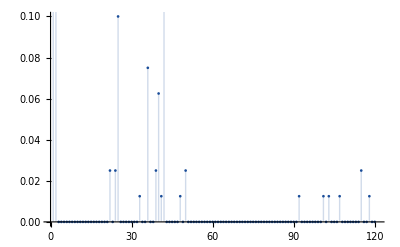

```mathematica
DiscretePlot[TimeAverage[5,5, 1][[k]],{k,1,120},PlotStyle-> {Orange,Thick,Directive[RGBColor[0.1,0.3,0.6]]},PlotRange->{{0,121},{0,0.1}}]
```

```mathematica
Position[Eigenvalues[N[CreateG2[4,Cycles[{{1,2}}],Cycles[{Range[1,Factorial[4]]}]]]],-1.+0.ⅈ]
```

{}

```mathematica
Position [Im[Eigenvalues[N[CreateG2[4,Cycles[{{1,2}}],Cycles[{Range[1,Factorial[4]]}]]]]],0.]
```

{{7},{20},{27},{28},{29},{32},{35},{38}}

```mathematica
{0.25951783377227894,-0.25951783377227894,0.8539115379498244,-0.8539115379498244,0.33227376861751134,-0.33227376861751134,0.,0.5208920600563669,-0.5208920600563669,0.20464016741217197,-0.20464016741217197,0.8265862891174638,-0.8265862891174638,0.1760309482972271,-0.1760309482972271,0.7243618462790667,-0.7243618462790667,0.7066216092176175,-0.7066216092176175,0.,0.8836449831106108,-0.8836449831106108,0.10462931861472924,-0.10462931861472924,0.9206902271135751,-0.9206902271135751,0.,0.,0.,0.10995987851929617,-0.10995987851929617,0.,0.9998500277956637,-0.9998500277956637,0.,0.41890362226403854,-0.41890362226403854,0.,0.9903154223086044,-0.9903154223086044,0.9914927206068853,-0.9914927206068853,0.3828121709779581,-0.3828121709779581,0.6294805045446467,-0.6294805045446467,0.45643899651785663,-0.45643899651785663}
```

```mathematica
Limt7 = TimeAverage[300,7, 1];
```

Find::stream: {1,2,3} is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

$Failed

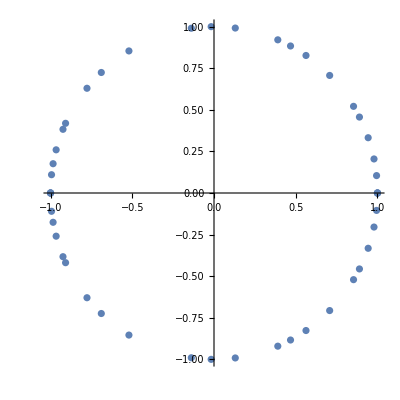

```mathematica
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@%363,AspectRatio->1]
```

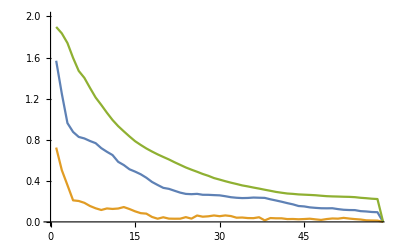

```mathematica
ListLinePlot[{ConverDist[500,60,4],ConverDist[500,60,3],ConverDist[500,60,5]},PlotRange->{{0,58},{0,2}}]
```

```mathematica
l= Table[TimeAverage[i,4,1], {i,{1,2,25}}];
```

```mathematica
l1= TimeAverage[120,4, 1];
j = Table[Flatten[Table[{i-> l[[k]][[i]]/Max[l[[k]]]},{i,1,24}]],{k,3}]
```

{{1→1.,2→0.,3→0.,4→0.,5→0.,6→0.,7→0.,8→0.,9→0.,10→0.,11→0.,12→0.,13→0.,14→0.,15→0.,16→0.,17→0.,18→0.,19→0.,20→0.,21→0.,22→0.,23→0.,24→0.},{1→1.,2→0.5,3→0.,4→0.,5→0.,6→0.,7→0.,8→0.,9→0.,10→0.,11→0.5,12→0.,13→0.,14→0.,15→0.,16→0.,17→0.,18→0.,19→0.,20→0.,21→0.,22→0.,23→0.,24→0.},{1→1.,2→0.744613,3→0.238378,4→0.351989,5→0.221461,6→0.466733,7→0.323045,8→0.235305,9→0.593213,10→0.226105,11→0.963623,12→0.693662,13→0.0839471,14→0.170112,15→0.602302,16→0.797362,17→0.0821416,18→0.339863,19→0.196221,20→0.309691,21→0.545337,22→0.299116,23→0.306138,24→0.370666}}

```mathematica
Table[Graph@CayleyGraph[PermutationGroup[{Cycles[{{1,2,3,4}}],Cycles[{{1,2}}]}],VertexStyle->White, EdgeStyle->Thick, VertexSize->j[[i]]],{i,3}]
```

{-Graphics-,-Graphics-,-Graphics-}

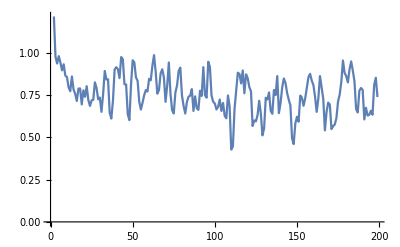

```mathematica
ListLinePlot[ConverDistI[400,200,4]]
```

```mathematica
Graph@CayleyGraph[PermutationGroup[{Cycles[{{1,2,3}}],Cycles[{{1,2}}]}],VertexStyle->White, EdgeStyle->Thick, VertexSize->j]
```

-Graphics-

```mathematica
CreateGX[4,Cycles[{{1,2}}],Cycles[{Range[1,Factorial[4]]}]];
```

```mathematica
TimeAverageX[3,4,1]
```

{0.416667,0.166667,0.,0.,0.,0.,0.,0.,0.0833333,0.,0.166667,0.0833333,0.,0.,0.,0.0833333,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
l1= Table[TimeAverageX[i,4,1], {i,{1,7,100}}];
```

```mathematica
j1 = Table[Flatten[Table[{i-> l1[[k]][[i]]/Max[l1[[k]]]},{i,1,24}]],{k,3}]
```

{{1→1.,2→0.,3→0.,4→0.,5→0.,6→0.,7→0.,8→0.,9→0.,10→0.,11→0.,12→0.,13→0.,14→0.,15→0.,16→0.,17→0.,18→0.,19→0.,20→0.,21→0.,22→0.,23→0.,24→0.},{1→1.,2→0.484536,3→0.0206186,4→0.175258,5→0.0103093,6→0.103093,7→0.0206186,8→0.0206186,9→0.319588,10→0.0103093,11→0.701031,12→0.216495,13→0.,14→0.0103093,15→0.154639,16→0.494845,17→0.,18→0.0309278,19→0.0206186,20→0.247423,21→0.175258,22→0.0927835,23→0.247423,24→0.0618557},{1→0.964099,2→1.,3→0.411517,4→0.520241,5→0.510317,6→0.502836,7→0.515978,8→0.415261,9→0.773304,10→0.504811,11→0.848503,12→0.696901,13→0.294519,14→0.378542,15→0.961001,16→0.744495,17→0.289717,18→0.445307,19→0.389829,20→0.593814,21→0.825547,22→0.518194,23→0.588005,24→0.45963}}

```mathematica
Table[Graph@CayleyGraph[PermutationGroup[{Cycles[{{1,2,3,4}}],Cycles[{{1,2}}]}],VertexStyle->White, EdgeStyle->Thick, VertexSize->j1[[i]]],{i,3}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
LimT=TimeAverage[10,7,1];
```

```mathematica
Tab11 = Table[ TimeAverage[i,6,1],{i,{2,10,20,30,40,50, 60,70}}];
LimT
```

$Aborted

```mathematica
Total[Abs[Tab11[[7]]- LimT]]
```

0.573877

```mathematica
Tab11[[8]]=TimeAverage[70,6,1]
```

Set::partw: Part 8 of {{0.5,0.25,0.,0.,0.,0.,0.,0.,0.,0.,«710»},«5»,{0.0234921,0.0122799,0.000513397,0.000678372,0.000584908,0.000805165,0.000800937,0.00165803,0.000825997,0.000800678,«710»}} does not exist.

```mathematica
Table[Total[Abs[Tab11⟦i⟧-LimT]],{i,1,8}]
```

{1.9773,1.6831,1.24025,0.947046,0.777512,0.658856,0.573877,0.502009}

```mathematica
Tab11[[5]]
```

Part::partw: Part 5 of {{0.133203,0.0666016,0.,0.,0.,0.,0.,0.000195312,0.,0.,«710»},{«1»},{0.0101,0.00564225,0.000941136,0.00127143,0.00182254,0.00154534,0.00225809,0.00143303,0.00110736,0.00133564,«710»}} does not exist.

```mathematica
LimT
```

```mathematica
Tab17 = Table[ TimeAverage[i,7,1],{i,{100,150, 200,250}}]
```

{{0.0135323,0.00687004,0.00013249,0.000121047,0.000180036,0.000113663,0.000101259,0.000145566,0.000125449,0.000106208,0.000148974,0.000172636,0.000159315,5014,0.000151053,0.000130665,0.000234192,0.0000948792,0.0001107,0.0000876629,0.000157898,0.000115621,0.000124712,0.000190088,0.00109124,0.000132218,0.000489944},1,1,{1}}
 |  |  |  |

```mathematica
Table[Total[Abs[Tab17⟦i⟧-Limt7]],{i,1,4}]
```

{0.413297,0.242628,0.14126,0.0680054}

```mathematica
Limit77 = TimeAverage[500,7, 1];
```

```mathematica
Table[Total[Abs[Tab17⟦i⟧-Limit77]],{i,1,4}]
```

{0.494388,0.335151,0.243821,0.179709}

```mathematica
Limit77
```

```mathematica
Export["simulation_n_7.csv",Tab17];
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["simulation_n_7.csv"]]]
```

```mathematica
customTable=Map[Append[#,";"]&,Tab17,{1}];
customTable1 = Map[Append[#,","]&,customTable,{2}];
```

Append::normal: Nonatomic expression expected at position 1 in Append[0.0135323,,].

Append::normal: Nonatomic expression expected at position 1 in Append[0.00687004,,].

Append::normal: Nonatomic expression expected at position 1 in Append[0.00013249,,].

General::stop: Further output of Append::normal will be suppressed during this calculation.

```mathematica
tableString=ExportString[customTable,"Table"];
```

```mathematica
Export["myCustomTable.csv",tableString,"Text"];
```

```mathematica
Limit55 = TimeAverage[700,5, 1];
```

```mathematica
%175
```

```mathematica
Tab15= Table[ TimeAverage[i,5,1],{i,{20,25,27,35}}];
```

```mathematica
Table[Total[Abs[Tab15⟦i⟧-Limit55]],{i,1,4}]
```

{0.668432,0.542222,0.49921,0.36617}

```mathematica
Limit66 = TimeAverage[720,6, 1];
```

```mathematica
Tab16= Table[ TimeAverage[i,6,1],{i,{76,77}}];
```

```mathematica
Table[Total[Abs[Tab16⟦i⟧-Limit66]],{i,1,2}]
```

{0.50121,0.495615}

```mathematica
Limit55 = TimeAverage[120,5, 1];
```

```mathematica
Tab15= Table[ TimeAverage[i,5,1],{i,{22,24,32,35}}];
```

```mathematica
Table[Total[Abs[Tab15⟦i⟧-Limit55]],{i,1,4}]
```

{0.547166,0.49517,0.336029,0.297994}

```mathematica
Limit44= TimeAverage[24,4, 1];
```

```mathematica
Tab14= Table[ TimeAverage[i,4,1],{i,{9,10,12,14}}];
```

```mathematica
Table[Total[Abs[Tab14⟦i⟧-Limit44]],{i,1,4}]
```

{0.536801,0.484943,0.40309,0.304172}

```mathematica
Limit33= TimeAverage[9,3, 1];
```

```mathematica
Tab13= Table[ TimeAverage[i,3,1],{i,{2,3,4,5}}];
```

```mathematica
Table[Total[Abs[Tab13⟦i⟧-Limit33]],{i,1,4}]
```

{0.735243,0.49566,0.349826,0.163542}

```mathematica
cgraph = CayleyGraph[PermutationGroup[{Cycles[{{1,2,3}}],Cycles[{{1,2}}]}]];
```

```mathematica
%222
```

```mathematica
Show[cgraph]
```